```mathematica
a=-1;
```

```mathematica
b=1;
f[x_]=Cos[x]^2;
n=5;
```

```mathematica
Do [{Subscript[x, k]=Cos[(π(2k+1))/(2(n+1))],Subscript[f, k]=f[Subscript[x, k]]},{k,0,n}]
```

```mathematica
Subscript[H, n][x_]=Subscript[f, 0]+∑_(j=1)^n (∑_(k=0)^j ((Subscript[f, k])/(( ∏_(i=0)^(k-1) (Subscript[x, k]-Subscript[x, i]))(∏_(i=k+1)^j (Subscript[x, k]-Subscript[x, i])))))∏_(m=0)^(j-1) (x-Subscript[x, m])//Expand//N
Tb1=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}]
Subscript[P, n][x_]=InterpolatingPolynomial[Tb1,x]//Expand//N
Subscript[P, n][x]-Subscript[H, n][x]
```

0.998753+5.32907×10^-15 x-0.977456 x^2-2.66454×10^-15 x^3+0.271788 x^4-1.77636×10^-15 x^5

{{(1+√3)/(2 √2),Cos[(1+√3)/(2 √2)]^2},{1/(√2),Cos[1/(√2)]^2},{(-1+√3)/(2 √2),Cos[(-1+√3)/(2 √2)]^2},{-(-1+√3)/(2 √2),Cos[(-1+√3)/(2 √2)]^2},{-1/(√2),Cos[1/(√2)]^2},{-(1+√3)/(2 √2),Cos[(1+√3)/(2 √2)]^2}}

0.998753-0.977456 x^2+8.88178×10^-16 x^3+0.271788 x^4

6.66134×10^-16-5.32907×10^-15 x-4.44089×10^-15 x^2+3.55271×10^-15 x^3-2.22045×10^-16 x^4+1.77636×10^-15 x^5

```mathematica
M1=Maximize[{D[f[x],{x,n+1}],a≤x≤b},x][[1]];
M2=Minimize[{D[f[x],{x,n+1}],a≤x≤b},x][[1]];
M=Max[Abs[M1],Abs[M2]]
R=M/((n+1)!*2^n)//N
```

32

0.00138889

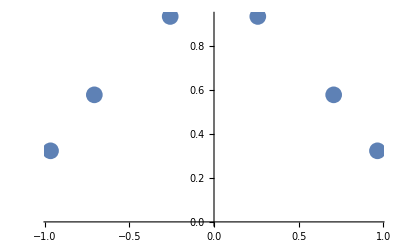

```mathematica
Gr1=ListPlot[Tb1,PlotStyle->PointSize[0.03]]
```

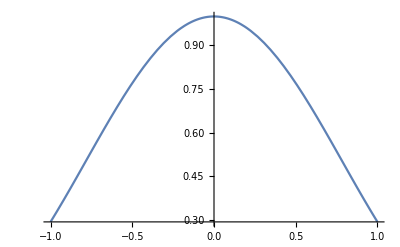

```mathematica
Gr2=Plot[f[x],{x,a,b}]
```

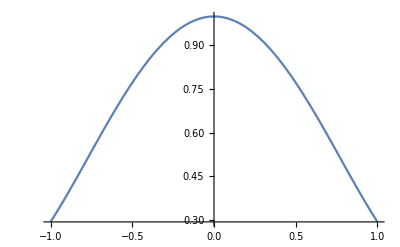

```mathematica
Gr3=Plot[Subscript[H, n][x],{x,a,b}]
```

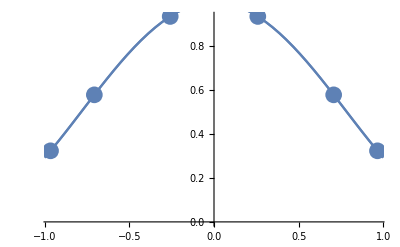

```mathematica
Show[Gr1,Gr2,Gr3]
```

```mathematica
a=0;
b=4;
f[x_]=Sin[2*x];
eps=10^-5;
n=1;
```

```mathematica
M1:=Maximize[{D[f[x],{x,n+1}],a≤x≤b},x][[1]];
M2:=Minimize[{D[f[x],{x,n+1}],a≤x≤b},x][[1]];
M:=Max[Abs[M1],Abs[M2]]
```

```mathematica
While[(R=(M(b-a)^(n+1))/((n+1)!2^(2n+1)))>eps,n=n+1]
n
Do[{Subscript[x, k]=((b-a)/2)*Cos[(π(2k+1))/(2(n+1))]+ (a+b)/2//N,Subscript[f, k]=f[Subscript[x, k]]},{k,0,n}]
```

12

```mathematica
Subscript[H, n][x_]=Subscript[f, 0]+∑_(j=1)^n (∑_(k=0)^j ((Subscript[f, k])/(( ∏_(i=0)^(k-1) (Subscript[x, k]-Subscript[x, i]))(∏_(i=k+1)^j (Subscript[x, k]-Subscript[x, i])))))∏_(m=0)^(j-1) (x-Subscript[x, m])//Expand//N
Tb1=Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}]
Subscript[P, n][x_]=InterpolatingPolynomial[Tb1,x]//Expand//N
Subscript[P, n][x]-Subscript[H, n][x]
```

-1.66602×10^-6+2.00014 x-0.00197839 x^2-1.32239 x^3-0.0315056 x^4+0.320725 x^5-0.0595451 x^6+0.0184507 x^7-0.0219364 x^8+0.00880322 x^9-0.00160055 x^10+0.000140303 x^11-4.84965×10^-6 x^12

{{3.98542,0.99318},{3.87003,0.993519},{3.64597,0.846166},{3.32625,0.360968},{2.92945,-0.411676},{2.47863,-0.970168},{2.,-0.756802},{1.52137,0.0986944},{1.07055,0.841733},{0.673755,0.975175},{0.354032,0.650365},{0.129968,0.257018},{0.0145823,0.0291604}}

-1.66602×10^-6+2.00014 x-0.00197839 x^2-1.32239 x^3-0.0315056 x^4+0.320725 x^5-0.0595451 x^6+0.0184507 x^7-0.0219364 x^8+0.00880322 x^9-0.00160055 x^10+0.000140303 x^11-4.84965×10^-6 x^12

-1.52145×10^-12-3.66462×10^-12 x+7.16721×10^-12 x^2-4.0461×10^-12 x^3+6.35603×10^-14 x^4+1.34076×10^-12 x^5-1.03614×10^-12 x^6+4.56427×10^-13 x^7-1.32706×10^-13 x^8+2.56375×10^-14 x^9-3.1353×10^-15 x^10+2.16244×10^-16 x^11-6.22823×10^-18 x^12

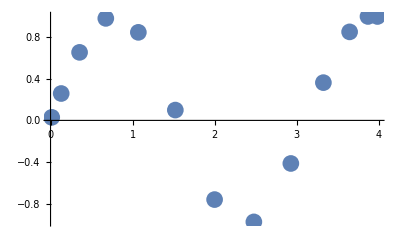

```mathematica
Gr1=ListPlot[Tb1,PlotStyle->PointSize[0.03]]
```

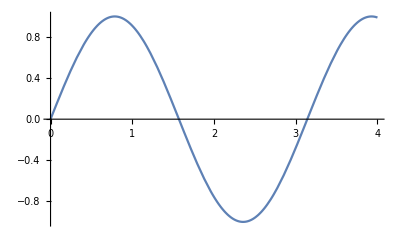

```mathematica
Gr2=Plot[f[x],{x,a,b}]
```

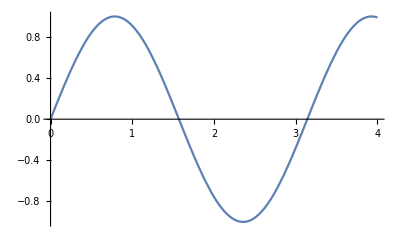

```mathematica
Gr3=Plot[Subscript[H, n][x],{x,a,b}]
```

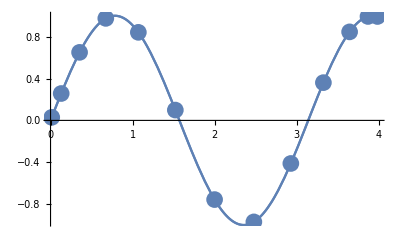

```mathematica
Show[Gr1,Gr2,Gr3]
```